```mathematica
Manipulate[
Module[{P,Psat,ϕω,relH,MW1,MW2,MW},
P=1;(*bar*)

Psat[T_]=(*100**)10^(5.40221-1838.675/(T+241.263));(*bar*)

ϕω[ϕ_,T_]=Abs[0.622*((ϕ*Psat[T])/(P-ϕ*Psat[T]))];
(*Style[Table[{ϕ,ϕω[ϕ,T]},{ϕ,0.2,1,0.2}],20]*)
MW1=28.(*97*);MW2=18.02;
MW=Which[mw==1,(MW1/MW2),mw==2,(MW2/MW1),mw==3,var];
(*relH[hum_,T_]=(MW1/MW2)*hum*P/Psat[T];*)
relH[ϕ_,T_]=MW*ϕ*Psat[T]/P;

Show[
Table[Plot[relH[ϕ,T],{T,x1,55},PlotRange->{{x1,55},{0,0.033}},AxesOrigin->{x1,0},AspectRatio->Full,ImageSize->500],{ϕ,0.1,1,0.1}],
Graphics[{Thick,Line[{{-10,0.033},{55,0.033}}],Line[{{33.25,0},{33.25,0.033}}]}],
PlotLabel->MW]

],
Control[{{mw,3,""},{1->" MW_1/MW_2 ",2->" MW_2/MW_1 ",3->" set "},Setter}],
Control[{{x1,5,"T1"},-10,20,5,Appearance->"Labeled"}],
PaneSelector[{3->Control[{{var,0.66,""},0.05,1,0.01,Appearance->"Labeled"}]},Dynamic@mw]
]
```

```mathematica
N[18/28]
```

0.642857

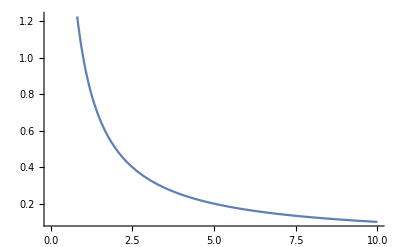

```mathematica
Plot[1/x,{x,0,10}]
```

```mathematica
Manipulate[
Module[{P,Psat,ϕω,relH,MW1,MW2,MW},
P=1;(*bar*)

Psat[T_]=10^(5.40221-1838.675/(T+241.263));(*bar*)

MW1=28;MW2=18;

relH[ϕ_,T_]=(MW2/MW1)*ϕ*Psat[T]/P;

Show[
Table[Plot[relH[ϕ,T],{T,x1,55},PlotRange->{{x1,55},{0,0.033}},AxesOrigin->{x1,0},AspectRatio->Full,ImageSize->500],{ϕ,0.1,1,0.1}],
Graphics[{Thick,Line[{{-10,0.033},{55,0.033}}],Line[{{33.25,0},{33.25,0.033}}]}]]

],
Control[{{x1,5,"T1"},-10,20,5,Appearance->"Labeled"}]
]
```